Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

1 - 6 Evaluation of Integrals
Show that the integral represents the indicated function. Hint. Use (5), p. 513, (10), or (11), p. 515; the integral tells you which one, and its value tells you what function to consider.

Three text panels are important enough to repeat here. The first is (4) from p. 513,
A(w) = 1/π∫_-π^π f(v)cos wvⅆv,                                       B(w) = 1/π∫_(-∞)^∞ f(v)sin wv ⅆv
The second is (10) from p. 515,
f(x) = ∫_0^∞ A(w)cos wxⅆw           where       A(w)= 2/π∫_0^∞ f(v)cos wvⅆv
The third is (11) from p. 515,
f(x) = ∫_0^∞ B(w)sin wx ⅆw           where       B(w) = 2/π∫_0^∞ f(v)sin wvⅆv

```mathematica
Clear["Global`*"]
```

1. ∫_0^∞ (cos xw+w sin xw)/(1+w^2)ⅆx = Piecewise[{{0, if x<0}, {π/2, if x=0}, {πⅇ^-x, if x>0}}]

```mathematica
∫_0^∞ (Cos[x w]+w Sin[x w])/(1+w^2)ⅆx
```

1/(1+w^2)

The above, integration by parts candidate, is taken care of automatically by Mathematica integration. But this is not the full answer. The s.m. advises to look at the stepwise summary, and the emphasized block on text panel (4) on p. 513. The bottom line in the stepwise summary is key. It relates to the domain subset of interest. So it is multiplied against each of the two expressions in the text block on p. 513. The two integrals below are the result, and the process of integrating them produces the full answer, green cells, as per text.

```mathematica
∫_0^∞ ⅇ^-v Cos[w v]ⅆv
```

ConditionalExpression[1/(1+w^2),Abs[Im[w]]<1]

```mathematica
∫_0^∞ ⅇ^-v Sin[w v]ⅆv
```

ConditionalExpression[w/(1+w^2),Abs[Im[w]]<1]

3.∫_0^∞ (1-cos πw)/w ⅆw = Piecewise[{{1/2 π, if 0<x<π}, {0, if x>π}}]

The Fourier integral normally has two parts. Depending on the function involved, one part may drop out. In problem 3 the displayed function is cos, an odd function. So it drops out, and the Fourier Sine Integral assumes predominance, as displayed in panel (11) on p. 515 of the text. The form the integral takes is below. The upper limit of the integal is changed to the max x domain value in the top line of the stepwise definition.

```mathematica
eqn1=2/π∫_0^π π/2 Sin[w v]ⅆv
```

(2 Sin[(π w)/2]^2)/w

```mathematica
exp2=(2 Sin[(π w)/2]^2)/w
```

(2 Sin[(π w)/2]^2)/w

```mathematica
exp21=exp2/.w->1
```

2

```mathematica
exp3=(1-Cos[π w])/w
```

(1-Cos[π w])/w

```mathematica
exp31=exp3/.w->1
```

2

Some test values of w demonstrate the equivalence of exp2 and exp3 above. The expressions are seen to be equivalent, related by the sin^2 x=(1-cos 2x)/2 trig identity. This makes the green cell above equal to the text answer.

5.∫_0^∞ (sin w-w cos w)/w^2 sin xwⅆw = Piecewise[{{1/2 πx, if 0<x<1}, {1/4 π, if x=1}, {0, if x>1}}]

The correct interpretation of this problem depends on seeing that it has as its template text panel (11). Then it is just a matter of assembling the parts from the right side of the equation. The coefficient 2/π is first added. The integral top limit is modified to reflect the max value of x, which is 1. The π/2 v represents the f(v) that is to be inserted into the expression of B(w). Note that the notation for the independent variable has changed from x to v to match the model. The remaining group, to the right, ( Sin[w v]ⅆv), consists of existing tokens. When the assembly is finished, it is integrated, and upon integration, it yields the main armature of the posed version of the problem. I was surprised when this turned out to resemble the left side B(w) of (11) so well. I was uncertain whether it would be required to actually do the integration. However, stripping the unessentials off the left version of B(w) on the left could not really be justified unless the integration revealed the final form. The green cells below show the separate parts of the text answer.

```mathematica
B(w)=2/π∫_0^1 π/2 v Sin[w v]ⅆv
```

```mathematica
2/π∫_0^1 π/2 v Sin[w v]ⅆv
```

(-w Cos[w]+Sin[w])/w^2

7 - 12 Fourier Cosine Integral Representations
Represent f(x) as an integral (10).

7. f(x) = Piecewise[{{1, if 0<x<1}, {0, if x>1}}]

This problem seems to have only a very small amount of explanatory material. It is covered in the s.m. however, so a path originating there seems like a good one to follow. Looking at the title of the problem subsection, it is Cosine Integral Representations, so this confirms the instruction to use panel (10). The right hand form in panel (10) is executed, the only change being the replacement of infinity by the max x value, 1. This ‘1’ is also the expression of the function to be added to the integral, the only description of a function of x that I have for this problem.

```mathematica
2/π∫_0^1 Cos[w v]ⅆv
```

(2 Sin[w])/(π w)

The above result is my A(w). So I proceed to insert this into the A(w) slot on the left side of panel (10),

```mathematica
f[x_]=∫_0^∞ (2 Sin[w])/(π w)Cos[w x]ⅆw
```

ConditionalExpression[1/2 (Sign[1-x]+Sign[1+x]),x∈Reals]

The green cell above matches the answer of the text. The actual result of integration is apparently not a matter of interest.

9. f(x) = 1/(1+x^2)  [x>0. Hint. See (13).]

The s.m. does not do this one. I will follow the same pattern and see if I can get the text answer. Here the definition of a function of x does not come from a domain restriction, but from a direct expression in the problem. I follow the template in (10), inserting the expression for x, altered to v:

```mathematica
A(w)=2/π∫_0^∞ (1Cos[w v])/(1+v^2)ⅆv
```

```mathematica
ConditionalExpression[ⅇ^(-Abs[w]),w∈Reals]
```

Both A(w) and the derived f(x) match the text answer.

11. f(x) = Piecewise[{{sin x, if 0<x<a}, {0, if x>a}}]

The correct answer is obtained if the upper limit on the right-side integral of panel (10) is set to π, but not if it is set to 1 or to a. What is the rationale for setting it to π?

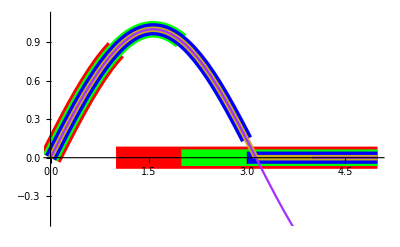

```mathematica
plot1 =Plot[Piecewise[{{Sin[x],0<x<1},{0,1<x}}],{x,0,5},PlotStyle->{Red,Thickness[0.04]}, PlotRange->{{0,5},{-.5,1.1}}];
plot2=Plot[Piecewise[{{Sin[x],0<x<2},{0,2<x}}],{x,0,5},
PlotStyle->{Green,Thickness[0.03]}, PlotRange->Full];
plot3=Plot[Piecewise[{{Sin[x],0<x<3},{0,3<x}}],{x,0,5},
PlotStyle->{Blue,Thickness[0.022]}, PlotRange->Full];
plot4=Plot[Piecewise[{{Sin[x],0<x<π},{0,π<x}}],{x,0,5},
PlotStyle->{RGBColor[.79,.666,.1],Thickness[0.01]}, PlotRange->Full];
plot5=Plot[Piecewise[{{Sin[x],0<x<4},{0,4<x}}],{x,0,5},
PlotStyle->{RGBColor[.643,.188,1],Thickness[0.004]}, PlotRange->Full];
Show[plot1,plot2,plot3,plot4,plot5]
```

```mathematica
Aw=2/π∫_0^π Sin[v]Cos[w v]ⅆv
```

(2 (1+Cos[π w]))/(π (1-w^2))

```mathematica
∫_0^∞ (2 (1+Cos[π w]))/(π-π w^2)(Cos[w x])ⅆw
```

Selecting π as the upper limit for the integral captures L, and this makes it a good choice to see the function and assess its character. It seems that the text wanted to select a value of a that would showcase the function, and L, via π, seems to fill the bill. The green cells above show the text answers for A(w) and f(x).

16 - 20 Fourier Sine Integral Representations
Represent f(x) as an integral (11).

```mathematica
17. f(x) = Piecewise[{{1, if 0<x<1}, {0, if x>1}}]
```

In this problem set I am referred to panel (11), which tells me it is about sine integrals. I may first wish to try the B(w) with v and upper limit set to:

```mathematica
bw=2/π∫_0^1 Sin[w v]ⅆv
```

(2 (1-Cos[w]))/(π w)

Inserting this B(w) value into the left-hand side of (11) I get:

```mathematica
fx=∫_0^∞ (2 (1-Cos[w]))/(π w)Sin[w x]ⅆw
```

Both B(w) and f(x) shown above agree with the text.

19. f(x) = Piecewise[{{ⅇ^x, if 0<x<1}, {0, if x>1}}]

Here are more ingredients to assemble a sine integral.

```mathematica
bw=∫_0^1 ⅇ^v Sin[w v]ⅆv
```

(w-ⅇ w Cos[w]+ⅇ Sin[w])/(1+w^2)

Notice that in shifting variables the ⅇ^x has become ⅇ^v. And again inserting this result into the left-hand side of (11) does the trick.

```mathematica
fx=2/π∫_0^∞ (w-ⅇ w Cos[w]+ⅇ Sin[w])/(1+w^2)Sin[x w]ⅆw
```

Which nails the text answer for f(x). (Answer for B(w) not given.)